```mathematica
subG = {gL-> s2W - 1/2,gR-> s2W};
subS2W={s2W-> 0.2324, ds2W-> 0.0083};
```

```mathematica
g1=gL^2;
g2=gR^2;
g3=(gL+1)^2;

(*Processes:A_i values for different scattering processes*)
Aνμ={1,(1-y)^2,0}; (*νμ e->νμ e*)
Aν̄μ={(1-y)^2,1,0}; (*ν̄μ e->ν̄μ e*)
Aνe={0,(1-y)^2,1}; (*νe e->νe e*)
Aν̄e={0,1,(1-y)^2}; (*ν̄e e->ν̄e e*)

(*Differential Cross-Section Function*)
σ[A_]:=(2 GF^2 Me Enu/π) (A[[1]] g1+A[[2]] g2+A[[3]] g3);
σtot[A_]:=Integrate[σ[A],{y,0,1}];
(*Calculate Differential Cross-Sections for each process*)
σνμ=σ[Aνμ];
σν̄μ=σ[Aν̄μ];
σνe=σ[Aνe];
σν̄e=σ[Aν̄e];

σtotνμ=σtot[Aνμ];
σtotν̄μ=σtot[Aν̄μ];
σtotνe=σtot[Aνe];
σtotν̄e=σtot[Aν̄e];
```

```mathematica
σμplus = σν̄μ + σνe//Simplify;
σμminus = σνμ + σν̄e//Simplify;
σtotμplus = σtotν̄μ + σtotνe//Simplify;
σtotμminus = σtotνμ + σtotν̄e//Simplify;
```

```mathematica
Rdiff=(σμplus - σμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify

Rtot=(σtotμplus - σtotμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify
```

-(3 s2W (-2+y) y)/(1+8 s2W^2)

(2 s2W)/(1+8 s2W^2)

```mathematica
dRtot=D[Rtot,{s2W}]*ds2W;
dRtot/Rtot/.subS2W
dRdiff=D[Rdiff,{s2W}]*ds2W
```

0.0141633

ds2W ((48 s2W^2 (-2+y) y)/((1+8 s2W^2)^2)-(3 (-2+y) y)/(1+8 s2W^2))

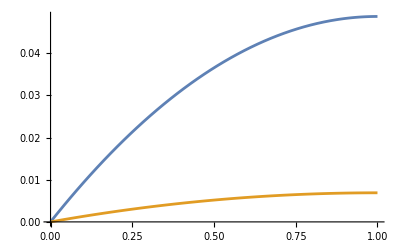

```mathematica
Plot[{0.1*Rdiff/.subS2W,dRdiff/.subS2W},{y,0,1}]//Simplify
```

```mathematica
`
```

```mathematica
Rdiff/.subS2W/.y-> 0
```

ReplaceAll::reps: {subS2W} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rdiff/.subS2W